# Q1

```mathematica
eqn1=u==α/(1+v^n)
```

u==α/(1+v^n)

```mathematica
f=-u+α/(1+v^n)
```

-u+α/(1+v^n)

```mathematica
eqn2=v==α/(1+u^n)
```

v==α/(1+u^n)

```mathematica
g=-v+α/(1+u^n)
```

-v+α/(1+u^n)

```mathematica
Solve[eqn2,u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→(-1+α/v)^(1/n)}}

## B & C

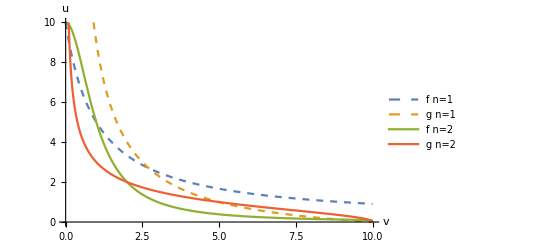

```mathematica
Plot[{α/(1+v^n)/.{α->10,n->1},(-1+α/v)^(1/n)/.{α->10,n->1},α/(1+v^n)/.{α->10,n->2},(-1+α/v)^(1/n)/.{α->10,n->2}},{v,0,10},AxesLabel->{"v","u"},PlotLegends->{"f n=1","g n=1","f n=2","g n=2"},PlotRange->{0,10},PlotStyle->{Dashed,Dashed,Thick,Thick}]
```

For n=1, there is just 1 s.s. For n=2, there are three s.s. As there is higher cooperatively, there are more steady states. For n=1, it is a stable steady state. For n=2, the middle steady state is unstable, but the two end steady states are stable

```mathematica
D[f,u]
```

-1

```mathematica
D[f,v]
```

-(n v^(-1+n) α)/((1+v^n)^2)

```mathematica
D[g,u]
```

-(n u^(-1+n) α)/((1+u^n)^2)

```mathematica
D[g,v]
```

-1

Find eigen values for n=1

```mathematica
Solve[(D[f,u]-λ)(D[g,v]-λ)-D[g,u]*D[f,v]==0,λ]/.{u->v,α->10,n->1}
```

{{λ→1/2 (-2-20/(1+v)^2)},{λ→1/2 (-2+20/(1+v)^2)}}

Solve for v-value for n=1 steady state. Plug this v-value into the expression above to find the eigen values.

```mathematica
NSolve[(α/(1+v^n)/.{α->10,n->1})==((-1+α/v)^(1/n)/.{α->10,n->1}),v]
```

{{v→-3.70156},{v→2.70156}}

```mathematica
{{λ->1/2 (-2-20/(1+v)^2)},{λ->1/2 (-2+20/(1+v)^2)}}/.v->2.70156
```

{{λ→-1.72984},{λ→-0.270155}}

Since both of these eigen values are less than 0, the 1 steady state in the n=1 case is stable
Find the eigen values for n=2

```mathematica
Solve[(D[f,u]-λ)(D[g,v]-λ)-D[g,u]*D[f,v]==0,λ]/.{u->v,α->10,n->2}
```

{{λ→1/2 (-2-(40 v)/((1+v^2)^2))},{λ→1/2 (-2+(40 v)/((1+v^2)^2))}}

Solve for v-value for n=2 steady state. Plug this v-value into the expression above to find the eigen values.

```mathematica
NSolve[(α/(1+v^n)/.{α->10,n->2})==((-1+α/v)^(1/n)/.{α->10,n->2}),v]
```

{{v→9.89898},{v→2.},{v→0.101021}}

```mathematica
{{λ->1/2 (-2-(40 v)/((1+v^2)^2))},{λ->1/2 (-2+(40 v)/((1+v^2)^2))}}/.v->2
```

{{λ→-13/5},{λ→3/5}}

Only one of these eigen values is less than 0, so this is an unstable steady sate.
The central steady state is stable for cooperativity of n=1, but it is unstable for n=2